```mathematica
n=3;
b0=(11*n)/(48*π^2);
b1=34/3(n/(16*π^2))^2;
R[β_]:=(β/(2*n*b0))^(b1/(2*b0^2))*Exp[-β/(4*n*b0)];
nTau=6;
```

```mathematica
β=5.7;
lambdaBeta=2.1947;
r1=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

0.671952

```mathematica
β=5.75;
lambdaBeta=2.087578;
r2=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

0.747222

```mathematica
β=5.8;
lambdaBeta=1.990720;
r3=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

0.828848

```mathematica
β=5.85;
lambdaBeta=1.905342;
r4=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

0.916049

```mathematica
β=5.9;
lambdaBeta=1.831481;
r5=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

1.00811

```mathematica
β=5.95;
lambdaBeta=1.768642;
r6=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

1.10434

```mathematica
β=6;
lambdaBeta=1.715383;
r7=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

1.20456

```mathematica
β=6.05;
lambdaBeta=1.670045;
r8=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

1.30894

```mathematica
β=6.1;
lambdaBeta=1.631051;
r9=(34.38*nTau*R[β]*lambdaBeta)^(-1)
```

1.41792

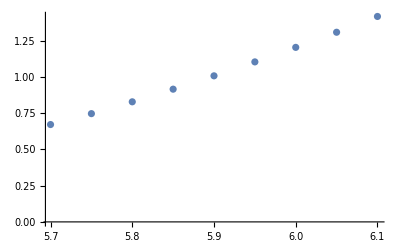

```mathematica
ListPlot[{{5.7,r1},{5.75,r2},{5.8,r3},{5.85,r4},{5.9,r5},{5.95,r6},{6,r7},{6.05,r8},{6.1,r9}}]
```